# NV-center qubits

## Connectivity : star Main ref: Abobeih

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu_develop"];
```

NV-center device, loaded after questlink

```mathematica
Get["../vqd.wl"];
```

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second
Frequency unit is  Hertz
Each qubit has unique characteristics

```mathematica
Options[NVCenterDelft]={
qubitsNum->6,
T1-> <|0-> 3600,1->60,2->60,3->60,4->60,5->60 |>,
(* we assume T2* echoed out to T2*)
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9,5->9|>,

(** Global magnetic field fluctuation due to^13 C bath 
Causes dephasing on the electron in 4 μs
External field is effectively perfect
**)
GlobalField-><|#->RandomReal[{-0.01,0.01}]&/@Range[0,5]|>,
(* ??? *)
GlobalFieldDetuning->66000,

(* rates are Hz. Direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins?*)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500,5->500|>,
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3,5->400*10^3|>,

(* 2-qubit gates can be done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 ,5->2*10^3|>,
(* approx 95-99 *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98 ,5->0.98|>,
(* fidelities are in percent and is obtained from random becnhmarking by default *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99,5->0.99 |>,
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999,4->0.999,6->0.99 |>,
(** Error ratio {depolarizing error, dephasing ratio}, where the ratios are sum to one. characterizes inhomogenieties between depolarizing and dephasing noises **)
(* For single rotations *)
EFSingleXY->{0.75,0.25},
(* For conditional rotations CRx and CRy. Note that, applying single rotations on nuclear spins mean applying conditional rotations *)
EFCRot->{0.9,0.1},
(** Initialization and destructive measurement on the electron spin.
nuclear spin init and measurement are done on the electron-spin through swap sequence **)
FidInit-> 0.999,
DurInit->2*10^-3,
(** measurements **)
FidMeas->0.946,
(* 10-20 μs *)
DurMeas->2*10^-5
};
```

## Introduction to essential elements

```mathematica
nvnode=NVCenterDelft[];
```

The native gates:

```mathematica
nvnode[Gates]⟦All,1⟧//Column
```

Init_(VQD`Private`q$_)/;VQD`Private`q$===0
M_(VQD`Private`q$_)/;VQD`Private`q$===0
Wait_(VQD`Private`qubits$__)[VQD`Private`dur$_]
Rz_(VQD`Private`q$_)[VQD`Private`θ$_]
Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0
Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0
Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0
Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0
CRx_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0
CRy_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0

## Common gates on nuclear spins obtained by sequence of native gates

```mathematica
(* cotrolled-pauli gates, where control qubits are the electron spins *)
Subscript[cX, c_,t_]:=Sequence@@{Subscript[CRx, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Rx, t][-π/2]}
Subscript[cY, c_,t_]:=Sequence@@{Subscript[CRy, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][-π/2]}
Subscript[cZ, c_,t_]:=Sequence@@{Subscript[Rx, t][π/2],Subscript[CRy, c,t][-π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][π/2],Subscript[Rx, t][-π/2]}
(* initialisation the nuclear spins *)
Subscript[initNcl, q_/;q>0]:=Sequence@@{Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Init, 0]}
(*measurement sequences on nuclear spins the computational basis *)
Subscript[measZ, q_/;q>0]:=Sequence@@{Subscript[Rx, 1][π/2],Subscript[Ry, 0][π/2],Subscript[CRy, 0,1][π/2],Subscript[Rx, 0][π/2],Subscript[M, 0]}
```

{Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2],Init_0}

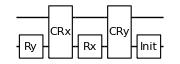

```mathematica
{Subscript[initNcl, 1]}
DrawCircuit@%
```

## 6 Qubits initialization

Initialize all qubits to zero

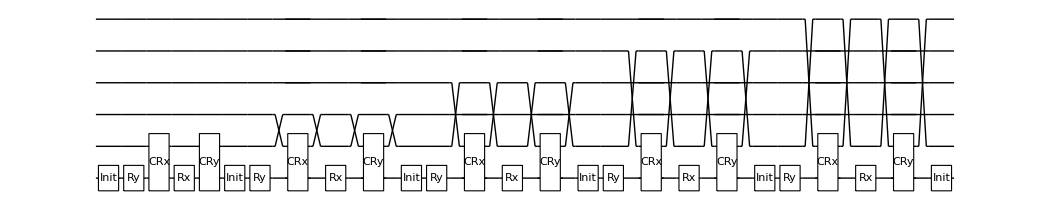

```mathematica
circInit={Subscript[Init, 0],Subscript[initNcl, 1],Subscript[initNcl, 2],Subscript[initNcl, 3],Subscript[initNcl, 4],Subscript[initNcl, 5]};
DrawCircuit[circInit]
```

```mathematica
ρ=CreateDensityQureg[6];
ρ2=CreateDensityQureg[6];
ψ=CreateQureg[6];
```

```mathematica
SetQuregMatrix[ρ,RandomMixState[6]];
CalcFidelity[ρ,InitZeroState@ψ]
```

0.0128535

Initialization on the noisy circuit. Serialize[circ] removes parallelism in the circuit.

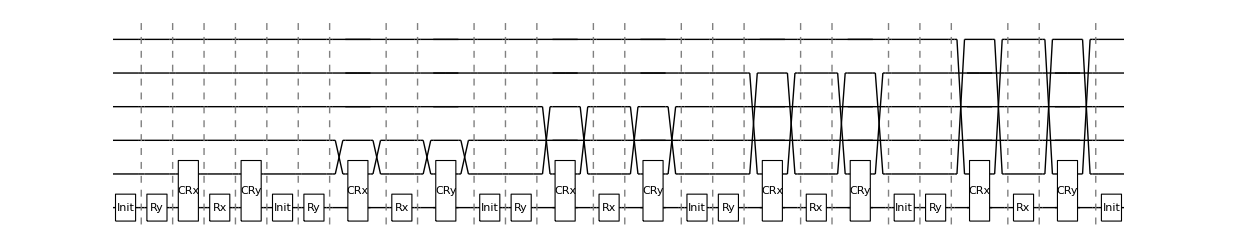

```mathematica
DrawCircuit@Serialize@circInit
```

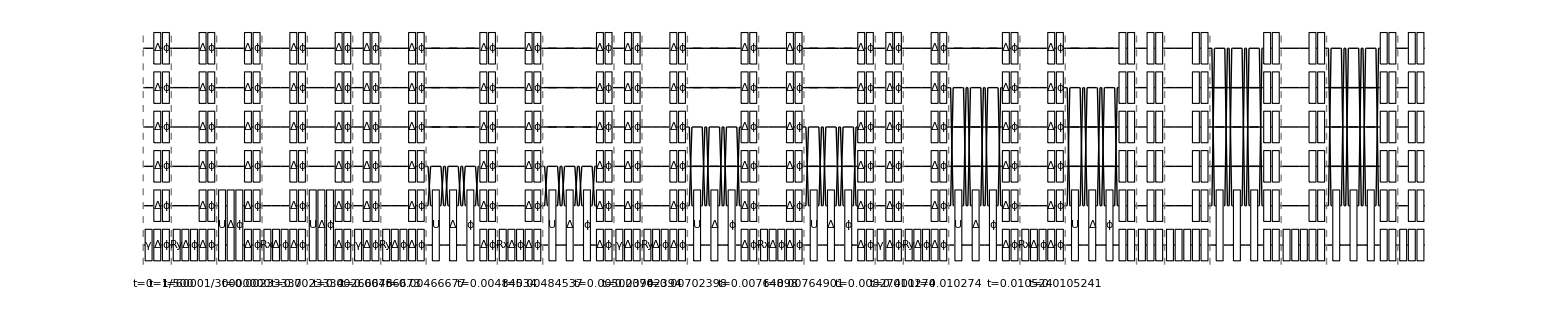

```mathematica
circInitOnDev=InsertCircuitNoise[Serialize@circInit,NVCenterDelft[],ReplaceAliases->True];
DrawCircuit[%,6]
```

```mathematica
ApplyCircuit[CloneQureg[ρ2,ρ],ExtractCircuit[circInitOnDev]];
CalcFidelity[ρ2,InitZeroState@ψ]
```

0.932498

```mathematica
DestroyAllQuregs[]
```

## Measurements

Measurements in the computational basis. Compare 4k shots of measurement to the fidelity set in the device

```mathematica
nshots=1000;
{ρ,ρinit}=CreateDensityQuregs[6,2];
```

#### On the electron spin

```mathematica
outputs=Flatten@Table[ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[M, 0]},NVCenterDelft[],ReplaceAliases->True]]
,{nshots}];
Print["correct outputs(0):"<>ToString[nshots-Total@outputs], "\nflipped outputs(1):"<>ToString[Total@outputs],"\nfidelity:"<>ToString[N[1-Total@outputs/nshots]*100]]
```

correct outputs(0):941
flipped outputs(1):59
fidelity:94.1

```mathematica
OptionValue[NVCenterDelft,FidMeas]
```

0.946

#### Measurement on the nuclear spins

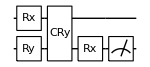

```mathematica
DrawCircuit[{Subscript[measZ, 1]}]
```

```mathematica
nshots=1000;
outputs=Flatten@Table[
ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[measZ, 1]},NVCenterDelft[],ReplaceAliases->True]],{nshots}];
Print["correct outputs(0):"<>ToString[nshots-Total@outputs], "\nflipped outputs(1):"<>ToString[Total@outputs],"\nfidelity:"<>ToString[N[1-Total[outputs]/nshots]*100]]
```

correct outputs(0):927
flipped outputs(1):73
fidelity:92.7

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
}
```

{t1→(9 ℏ)/J,t2→(18 ℏ)/J,Γ→0.1,ω→(5 J)/3}

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The time-dependent gap Δ is controlled through g(t)

```mathematica
τs=Join[Range[0,7,0.4],Range[7,11,0.04],Range[11.4,17,0.4],Range[17,21,0.04],Range[21.04,27.04,0.4]]
```

{0.,0.4,0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.,7.04,7.08,7.12,7.16,7.2,7.24,7.28,7.32,7.36,7.4,7.44,7.48,7.52,7.56,7.6,7.64,7.68,7.72,7.76,7.8,7.84,7.88,7.92,7.96,8.,8.04,8.08,8.12,8.16,8.2,8.24,8.28,8.32,8.36,8.4,8.44,8.48,8.52,8.56,8.6,8.64,8.68,8.72,8.76,8.8,8.84,8.88,8.92,8.96,9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.4,11.8,12.2,12.6,13.,13.4,13.8,14.2,14.6,15.,15.4,15.8,16.2,16.6,17.,17.,17.04,17.08,17.12,17.16,17.2,17.24,17.28,17.32,17.36,17.4,17.44,17.48,17.52,17.56,17.6,17.64,17.68,17.72,17.76,17.8,17.84,17.88,17.92,17.96,18.,18.04,18.08,18.12,18.16,18.2,18.24,18.28,18.32,18.36,18.4,18.44,18.48,18.52,18.56,18.6,18.64,18.68,18.72,18.76,18.8,18.84,18.88,18.92,18.96,19.,19.04,19.08,19.12,19.16,19.2,19.24,19.28,19.32,19.36,19.4,19.44,19.48,19.52,19.56,19.6,19.64,19.68,19.72,19.76,19.8,19.84,19.88,19.92,19.96,20.,20.04,20.08,20.12,20.16,20.2,20.24,20.28,20.32,20.36,20.4,20.44,20.48,20.52,20.56,20.6,20.64,20.68,20.72,20.76,20.8,20.84,20.88,20.92,20.96,21.,21.04,21.44,21.84,22.24,22.64,23.04,23.44,23.84,24.24,24.64,25.04,25.44,25.84,26.24,26.64,27.04}

```mathematica
Length@τs
```

251

```mathematica
(*τ=t J/ℏ*)
```

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τ2)//.constants,J>0];
```

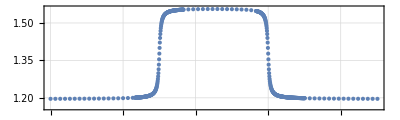

```mathematica
ListPlot[Transpose@{τ2,gvals},PlotRange->{1.16,1.56},Joined->False,PlotTheme->"Detailed",AspectRatio->0.3]
```

First part: Gaudin Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
expGaudin[q_,n_,ϵ_,t_]:=With[{g=coupling[t,g0,gc]},
ExpandAll@Simplify[(g*ϵ[[q+1]]*Hgaudin[q,n,ϵ,g]/ℏ)/.constants,J>0]]

Ugaudin[q_,n_,ϵ_,τ_]:=Subscript[U, Sequence@@Range[0,n-1]][MatrixExp[I*τ*CalcPauliStringMatrix[ExpandAll[(expGaudin[q, n, ϵ, τ ℏ/Δ0]*ℏ/Δ0) /. constants]]]]
```

Second part: Ising Hamiltonian

```mathematica
Uising[τ_,n_]:=Module[{g=coupling[τ*ℏ/Δ0,g0,gc],exp},
exp=Flatten@Table[If[j!=k,Simplify[( g/(Δ0*4) If[And[j<n-1,k<n-1],Subscript[Z, j] Subscript[Z, k] Subscript[Id, n-1],Subscript[Z, j] Subscript[Z, k]])/.constants,J>0],{}],
{j,0,n-1},{k,0,n-1}];
Subscript[U, Sequence@@Range[0,n-1]][MatrixExp[-ⅈ τ CalcPauliStringMatrix[#]]]&/@exp
]
```

Third part: single qubits Hamiltonian

```mathematica
Usingle[τ_,n_]:=Table[Subscript[Rz, j][Simplify[(τ/Δ0 coupling[τ*ℏ/Δ0,g0,gc])/.constants,J>0] ],{j,0,n-1}]
```

The analytic values

```mathematica
τs
```

{0.,0.4,0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.,7.04,7.08,7.12,7.16,7.2,7.24,7.28,7.32,7.36,7.4,7.44,7.48,7.52,7.56,7.6,7.64,7.68,7.72,7.76,7.8,7.84,7.88,7.92,7.96,8.,8.04,8.08,8.12,8.16,8.2,8.24,8.28,8.32,8.36,8.4,8.44,8.48,8.52,8.56,8.6,8.64,8.68,8.72,8.76,8.8,8.84,8.88,8.92,8.96,9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.4,11.8,12.2,12.6,13.,13.4,13.8,14.2,14.6,15.,15.4,15.8,16.2,16.6,17.,17.,17.04,17.08,17.12,17.16,17.2,17.24,17.28,17.32,17.36,17.4,17.44,17.48,17.52,17.56,17.6,17.64,17.68,17.72,17.76,17.8,17.84,17.88,17.92,17.96,18.,18.04,18.08,18.12,18.16,18.2,18.24,18.28,18.32,18.36,18.4,18.44,18.48,18.52,18.56,18.6,18.64,18.68,18.72,18.76,18.8,18.84,18.88,18.92,18.96,19.,19.04,19.08,19.12,19.16,19.2,19.24,19.28,19.32,19.36,19.4,19.44,19.48,19.52,19.56,19.6,19.64,19.68,19.72,19.76,19.8,19.84,19.88,19.92,19.96,20.,20.04,20.08,20.12,20.16,20.2,20.24,20.28,20.32,20.36,20.4,20.44,20.48,20.52,20.56,20.6,20.64,20.68,20.72,20.76,20.8,20.84,20.88,20.92,20.96,21.,21.04,21.44,21.84,22.24,22.64,23.04,23.44,23.84,24.24,24.64,25.04,25.44,25.84,26.24,26.64,27.04}

```mathematica
ugaudin = Table[Ugaudin[#, 5, ϵ, τ] & /@ Range[0, 4], {τ, τs}];
uising = Table[Uising[τ, 5], {τ, τs}];
usingle = Table[Usingle[τ, 5], {τ, τs}];
uanalytic = <|"τ" -> τs, "ugaudin" -> ugaudin, "uising" -> uising, "usingle" -> usingle|>;
DumpSave["uanalytic.mx", uanalytic];
```

$Aborted

$Aborted

$Aborted

```mathematica
uanalytic<<uanaltic.mx;
```

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0]
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=0.5(1+ϵ/ej)/.constants
vjs=0.5(1-ϵ/ej)/.constants
```

{1.30171 J,2.69258 J,4.28499 J,5.91843 J,7.56637 J}

{0.820092,0.964238,0.986194,0.992811,0.995614}

{0.179908,0.0357617,0.0138063,0.00718887,0.00438605}

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs
(* double check *)
2*ArcSin@Sqrt@vjs
```

{0.876058,0.380506,0.235545,0.169778,0.132552}

{0.876058,0.380506,0.235545,0.169778,0.132552}

```mathematica
DestroyAllQuregs[]
{ψinit,ψ}=CreateQuregs[5,2];
```

```mathematica
(* BCS *)
ApplyCircuit[InitZeroState@ψinit,Table[Subscript[Ry, j-1][θinit[[j]]],{j,5}]];
```

```mathematica
(* Rmf(τ)*)
rmf=Table[
bcscirc=Flatten@{ugaudin[[j]],uising[[j]],usingle[[j]]};
ApplyCircuit[CloneQureg[ψ,ψinit],bcscirc];
{τs[[j]],CalcFidelity[ψ,ψinit]}
,{j,Length@τs}];
```

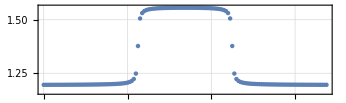

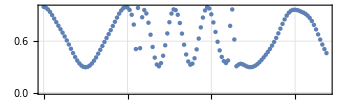

```mathematica
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->False,PlotTheme->"Detailed",AspectRatio->0.3]
ListPlot[rmf,PlotRange->All,Joined->False,PlotTheme->"Detailed",AspectRatio->0.3]
```

```mathematica
τs
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,20.2,20.4,20.6,20.8,21.,21.2,21.4,21.6,21.8,22.,22.2,22.4,22.6,22.8,23.,23.2,23.4,23.6,23.8,24.,24.2,24.4,24.6,24.8,25.,25.2,25.4,25.6,25.8,26.,26.2,26.4,26.6,26.8,27.}